```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

VII.1 Quantizing Yang-Mills Theory

```mathematica
PR1["The Faddeev-Popov method where: ",
(tmp0={{𝒵->IntegralOp[{A}, Exp[I S[A]]. Δ[A] . δ[f[A]]],"Converted partitian function."},
{S[A]->IntegralOp[{x},ℒ],"Action"},
{Δ[A]->1/IntegralOp[{g},δ[f[Ad[g]]]],"determinant of A"},
{Subscript[A, g]->g.A.g^-1-I xPartialD[g,x].g^-1,"gauge transform"},
g->g[x]
})//Column,NL,
"Step to (4) with ",sub=f[A]->xPartialD[A,x]-σ,Yield,
tmp=tmp0[[4]]
]
```

The Faddeev-Popov method where: {𝒵→∫_A [ⅇ^(ⅈ S[A]).Δ[A].δ[f[A]]],Converted partitian function.}
{S[A]→∫_x [ℒ],Action}
{Δ[A]→1/(∫_g [δ[f[Ad[g]]]]),determinant of A}
{A_g→-ⅈ UnderBar[∂]_x[g].1/g+g.A.1/g,gauge transform}
g→g[x]
Step to (4) with f[A]→-σ+UnderBar[∂]_x[A]
→ {A_g→-ⅈ UnderBar[∂]_x[g].1/g+g.A.1/g,gauge transform}

```mathematica
PR1[CO["VII.1.1:  The gauge choice in the text preserves Lorentz invariance.  It is often useful to choose a gauge that breaks Lorentz invariance, for example, ", f[A]->n@u[μ]  T[A,"d"][μ][x]," with n some fixed 4-vector.  This class of gauge choices, known as the axial gauge, contains various popular gauges, each of which corresponds to a particular choice of n.  For instance, in light-cone gauge, ",n->{{1,0,0,1}}," in space-cone gauge, ",n->{{0,1,I,0}},"."," Show that for any given A[x] we can find a gauge transformations so that ",n.A'[x]->0
]
]
```

VII.1.1:  The gauge choice in the text preserves Lorentz invariance.  It is often useful to choose a gauge that breaks Lorentz invariance, for example, f[A]→n_μ^μ A_μ^μ[x] with n some fixed 4-vector.  This class of gauge choices, known as the axial gauge, contains various popular gauges, each of which corresponds to a particular choice of n.  For instance, in light-cone gauge, n→{{1,0,0,1}} in space-cone gauge, n→{{0,1,ⅈ,0}}. Show that for any given A[x] we can find a gauge transformations so that n.A'[x]→0

```mathematica
PR1["Problem: Is it is possible to find a gauge transformation, U, such that ",tmp0={T[A',"d",{μ}]->SuperDagger[U].A@d[μ].U+I SuperDagger[U].xPartialD[U,μ],
n@u[μ].T[A',"d",{μ}]->0,ForAny[n@u[μ]]},
NL,"Since: ",tmp=tmp0[[2]],
imply,tmp=tmp/.tmp0[[1]],
imply,tmp=tmp//.simpleDot2[{n@u[_]}],
Imply,"Look for U ∍ ",forAny[A@d[μ],n@u[μ]],yield,tmpn=tmp/.SuperDagger[U]->1//.simpleDot2[{n@u[_]}],
NL,"Define relative distance of r to x in direction n as: ",
subλ=λ[x]->r.x/(r.n),
imply,{x->λ[x]n+x@d["⊥"],r.x@d["⊥"]->0},
Yield,subλdμ=Map[xPartialD[#,μ]&,subλ],
yield,subλdμ=(subλdμ//DerivativeExpand[{r,n}])//.simpleDot2[{}] ,
yield,subλdμ={subλdμ,r . xPartialD[x,a_]->r@d[a],r@d[a_] n@u[a_]->r.n},
"xPOFF",
NL,"Verify satisfying gauge transformation: ",
subU=U[x]->Exp[-I IntegralOp[{{σ,0,λ[x]}},n.A[σ.n+x@d["⊥"]]]],
Imply,tmp=tmpn/.Dot->Times/.T[A,"d",{μ}]n@u[μ]->n.A[x]/.U->U[x]/.subU,
Imply,tmp=tmp//DerivativeExpand[{n}],
NL,"Using: ",sub=xPartialD[IntegralOp[{{a_,a0_,a1_}},b_],c_]:>IntegralOp[{{a,a0,a1}},xPartialD[b,c]]-((b xPartialD[a0,c])/.a->a0)+((b xPartialD[a1,c])/.a->a1),
Imply,tmp=tmp/.sub/.xn.A[i_]->n@u[ν]T[A,"d"][ν][i],
Imply,xtmp=tmp=tmp//DerivativeExpand[{n}],
"PONdd",
Imply,tmp=tmp/.simpleDot2[{}]/.IntegralOp[_,0]->0//Expand//Collect[#,Exp[_]]&,
NL,"Examine term in ():",
Yield,tmp=tmp[[1,2]],
Yield,tmp=tmp/.Dot[n,xPartialD[b_,c_]]->xPartialD[n . b,c],
Yield,tmp=tmp//.subλdμ,
Imply,tmp=tmp/.n@u[μ]IntegralOp[{{a_,a0_,a1_}},xPartialD[c_,d_]]:>(c/.a->a1)-(c/.a->a0)//.simpleDot2[{}],
CR["???"]
];
```

Problem: Is it is possible to find a gauge transformation, U, such that {A'_μ^μ→ⅈ U^†.UnderBar[∂]_μ[U]+U^†.A_μ^μ.U,n_μ^μ.A'_μ^μ→0,ForAny[n_μ^μ]}
Since: n_μ^μ.A'_μ^μ→0 ⇒ n_μ^μ.(ⅈ U^†.UnderBar[∂]_μ[U]+U^†.A_μ^μ.U)→0 ⇒ ⅈ U^†.UnderBar[∂]_μ[U] n_μ^μ+U^†.A_μ^μ.U n_μ^μ→0
⇒ Look for U ∍ forAny[A_μ^μ,n_μ^μ] ⟶ A_μ^μ.U n_μ^μ+ⅈ n_μ^μ UnderBar[∂]_μ[U]→0
Define relative distance of r to x in direction n as: λ[x]→(r.x)/(r.n) ⇒ {x→x_⊥^⊥+n λ[x],r.x_⊥^⊥→0}
→ UnderBar[∂]_μ[λ[x]]→UnderBar[∂]_μ[(r.x)/(r.n)] ⟶ UnderBar[∂]_μ[λ[x]]→(r.UnderBar[∂]_μ[x])/(r.n) ⟶ {UnderBar[∂]_μ[λ[x]]→(r.UnderBar[∂]_μ[x])/(r.n),r.UnderBar[∂]_a_[x]→r_a^a,n_a_^a_ r_a_^a_→r.n}xPOFF
Verify satisfying gauge transformation: U[x]→ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]])
⇒ ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n.A[x]+ⅈ n_μ^μ UnderBar[∂]_μ[ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]])]→0
⇒ ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n.A[x]+ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n_μ^μ UnderBar[∂]_μ[∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]]→0
Using: UnderBar[∂]_c_[∫_{a_,a0_,a1_} [b_]]:>∫_{a,a0,a1} [UnderBar[∂]_c[b]]-(b UnderBar[∂]_c[a0]/.a→a0)+(b UnderBar[∂]_c[a1]/.a→a1)
⇒ ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n.A[x]+ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n_μ^μ (∫_{σ,0,λ[x]} [UnderBar[∂]_μ[n.A[σ.n+x_⊥^⊥]]]-n.A[0.n+x_⊥^⊥] UnderBar[∂]_μ[0]+n.A[λ[x].n+x_⊥^⊥] UnderBar[∂]_μ[λ[x]])→0
⇒ ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n.A[x]+ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) n_μ^μ (∫_{σ,0,λ[x]} [0.A[σ.n+x_⊥^⊥]+n.UnderBar[∂]_μ[A[σ.n+x_⊥^⊥]]]+n.A[λ[x].n+x_⊥^⊥] UnderBar[∂]_μ[λ[x]])→0PONdd
⇒ ⅇ^(-ⅈ ∫_{σ,0,λ[x]} [n.A[σ.n+x_⊥^⊥]]) (n.A[x]+∫_{σ,0,λ[x]} [n.UnderBar[∂]_μ[A[σ.n+x_⊥^⊥]]] n_μ^μ+n.A[λ[x].n+x_⊥^⊥] n_μ^μ UnderBar[∂]_μ[λ[x]])→0
Examine term in ():
→ n.A[x]+∫_{σ,0,λ[x]} [n.UnderBar[∂]_μ[A[σ.n+x_⊥^⊥]]] n_μ^μ+n.A[λ[x].n+x_⊥^⊥] n_μ^μ UnderBar[∂]_μ[λ[x]]
→ n.A[x]+∫_{σ,0,λ[x]} [UnderBar[∂]_μ[n.A[σ.n+x_⊥^⊥]]] n_μ^μ+n.A[λ[x].n+x_⊥^⊥] n_μ^μ UnderBar[∂]_μ[λ[x]]
→ n.A[x]+n.A[λ[x].n+x_⊥^⊥]+∫_{σ,0,λ[x]} [UnderBar[∂]_μ[n.A[σ.n+x_⊥^⊥]]] n_μ^μ
⇒ n.A[x]-n.A[x_⊥^⊥]+2 n.A[λ[x].n+x_⊥^⊥]???

```mathematica
Com:=MCommutator; DefineTensor[U,V]; Vd[i_]:=T[V,"d"][i]
PR1[CO["Derive (17) and relate f to the coupling g in the continuum formulation of Yang-Mills theory.  Use the Baker-Campbell-Hausdorff formula: ",
subBCH=Exp[A_].Exp[B_]->Exp[A+B+Com[A,B]/2+(Com[A,Com[A,B]]+Com[B,Com[B,A]])/12]],

Imply,"(17) (where μ[i,j] also indicates from i->j) is: ",
(tmp0={
e17=Tr[U@dd[i,j]. U@dd[j,k]. U@dd[k,l]. U@dd[l,i]]->Tr[Exp[I a^2 F@dd[μ,ν]+xOrd[a^3]]],
U@dd[i_,j_]->SuperDagger[T[V,"d"][i]].  Exp[I a T[ A,"d"][μ[i,j]][x]].V@d[j]
})//Column,

Imply,tmp=tmp0[[1]]/.tmp0[[2]],
NL,"Eliminate V's by using cyclic property of the arguements of Tr and unitarity of V's",
sub={SuperDagger[a_] . b__ . a_->b.a.SuperDagger[a],a_ .SuperDagger[a_]->1},
Imply,tmp0=tmp//. sub//.simpleDot2[{}]
]
```

Derive (17) and relate f to the coupling g in the continuum formulation of Yang-Mills theory.  Use the Baker-Campbell-Hausdorff formula: ⅇ^A_.ⅇ^B_→ⅇ^(A+B+1/2 (A.B-B.A)+1/12 (A.(A.B-B.A)+B.(-A.B+B.A)-(A.B-B.A).A-(-A.B+B.A).B))
⇒ (17) (where μ[i,j] also indicates from i->j) is: Tr[U_ij^ij.U_jk^jk.U_kl^kl.U_li^li]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
U_i_j_^i_j_→(V_i^i)^†.ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).V_j^j
⇒ Tr[(V_i^i)^†.ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).V_j^j.(V_j^j)^†.ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).V_k^k.(V_k^k)^†.ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).V_l^l.(V_l^l)^†.ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x]).V_i^i]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
Eliminate V's by using cyclic property of the arguements of Tr and unitarity of V's{a_^†.b__.a_→b.a.a^†,a_.a_^†→1}
⇒ Tr[ⅇ^(ⅈ a A_μ[i,j]^μ[i,j][x]).ⅇ^(ⅈ a A_μ[j,k]^μ[j,k][x]).ⅇ^(ⅈ a A_μ[k,l]^μ[k,l][x]).ⅇ^(ⅈ a A_μ[l,i]^μ[l,i][x])]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]

```mathematica
PR1["We expand the BCF formula to 4 elements.  The BCF formula to first order: ",
Yield,sub=Exp[A_].Exp[B_]:>Exp[A+B+Com[A,B]/2],
"POFF",
Imply,tmp=Exp[A].Exp[B].Exp[C].Exp[D],
Imply,tmp=tmp->
((Exp[A].Exp[B]/.sub).(Exp[C].Exp[D]/.sub)/.sub/.aa:A|B|C|D->λ aa)//Expand//RuleX2PatternVar[{A,B,C,D}],
Imply,tmp=tmp//.simpleDot2[{λ}]//ExpandAll,
"PON",
Imply,subBCF1=tmp/.λ^(3|4)->0/.λ->1//Simplify
]
```

We expand the BCF formula to 4 elements.  The BCF formula to first order: 
→ ⅇ^A_.ⅇ^B_:>Exp[A+B+1/2 Com[A,B]]
⇒ ⅇ^A_.ⅇ^B_.ⅇ^C_.ⅇ^D_→ⅇ^(1/2 (2 A+2 B+2 C+2 D+A.B+A.C+A.D-B.A+B.C+B.D-C.A-C.B+C.D-D.A-D.B-D.C))

```mathematica
PR1["Apply BCF formula: ",tmp=tmp0/.subBCF1,
NL,"Simplify by relabeling μ: ",
sub={μ[i,j]->μ[1],μ[j,k]->μ[2],μ[k,l]->μ[3],μ[l,i]->μ[4]},
Yield,tmp=tmp//.sub//.simpleDot2[{a}]//Simplify,
NL,"First order approximation of A at x to relative center of plaqette (0): ",
"POFF",
Yield,subA=A[x]->(Series[A[x],{x,0,1}]  /.x->x@u[ν]/.A_'->xPartialD[A,ν]//Normal),
"PON",
Yield,subA=subA/.A->T[A,"d"][μ]/.A_'->xPartialD[A,ν]//Normal//RuleX2PatternVar[{ν,μ}],
Imply,tmp=tmp//.subA,
NL,"Simplify notation: remove [0], contract ∂_μ A: ",
sub={a_[0]->a,x@u[a_]xPartialD[A_,a_]->xPartialD[A,x]},
Imply,tmp1=tmp//.sub
];
```

Apply BCF formula: Tr[ⅇ^(1/2 ((ⅈ a A_μ[i,j]^μ[i,j][x]).(ⅈ a A_μ[j,k]^μ[j,k][x])+(ⅈ a A_μ[i,j]^μ[i,j][x]).(ⅈ a A_μ[k,l]^μ[k,l][x])+(ⅈ a A_μ[i,j]^μ[i,j][x]).(ⅈ a A_μ[l,i]^μ[l,i][x])-(ⅈ a A_μ[j,k]^μ[j,k][x]).(ⅈ a A_μ[i,j]^μ[i,j][x])+(ⅈ a A_μ[j,k]^μ[j,k][x]).(ⅈ a A_μ[k,l]^μ[k,l][x])+(ⅈ a A_μ[j,k]^μ[j,k][x]).(ⅈ a A_μ[l,i]^μ[l,i][x])-(ⅈ a A_μ[k,l]^μ[k,l][x]).(ⅈ a A_μ[i,j]^μ[i,j][x])-(ⅈ a A_μ[k,l]^μ[k,l][x]).(ⅈ a A_μ[j,k]^μ[j,k][x])+(ⅈ a A_μ[k,l]^μ[k,l][x]).(ⅈ a A_μ[l,i]^μ[l,i][x])-(ⅈ a A_μ[l,i]^μ[l,i][x]).(ⅈ a A_μ[i,j]^μ[i,j][x])-(ⅈ a A_μ[l,i]^μ[l,i][x]).(ⅈ a A_μ[j,k]^μ[j,k][x])-(ⅈ a A_μ[l,i]^μ[l,i][x]).(ⅈ a A_μ[k,l]^μ[k,l][x])+2 ⅈ a A_μ[i,j]^μ[i,j][x]+2 ⅈ a A_μ[j,k]^μ[j,k][x]+2 ⅈ a A_μ[k,l]^μ[k,l][x]+2 ⅈ a A_μ[l,i]^μ[l,i][x]))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
Simplify by relabeling μ: {μ[i,j]→μ[1],μ[j,k]→μ[2],μ[k,l]→μ[3],μ[l,i]→μ[4]}
→ Tr[ⅇ^(-1/2 a (a A_μ[1]^μ[1][x].A_μ[2]^μ[2][x]+a A_μ[1]^μ[1][x].A_μ[3]^μ[3][x]+a A_μ[1]^μ[1][x].A_μ[4]^μ[4][x]-a A_μ[2]^μ[2][x].A_μ[1]^μ[1][x]+a A_μ[2]^μ[2][x].A_μ[3]^μ[3][x]+a A_μ[2]^μ[2][x].A_μ[4]^μ[4][x]-a A_μ[3]^μ[3][x].A_μ[1]^μ[1][x]-a A_μ[3]^μ[3][x].A_μ[2]^μ[2][x]+a A_μ[3]^μ[3][x].A_μ[4]^μ[4][x]-a A_μ[4]^μ[4][x].A_μ[1]^μ[1][x]-a A_μ[4]^μ[4][x].A_μ[2]^μ[2][x]-a A_μ[4]^μ[4][x].A_μ[3]^μ[3][x]-2 ⅈ A_μ[1]^μ[1][x]-2 ⅈ A_μ[2]^μ[2][x]-2 ⅈ A_μ[3]^μ[3][x]-2 ⅈ A_μ[4]^μ[4][x]))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
First order approximation of A at x to relative center of plaqette (0): 
→ A_μ_^μ_[x]→A_μ^μ[0]+x_ν^ν UnderBar[∂]_ν[A_μ^μ][0]
⇒ Tr[ⅇ^(-1/2 a (a (A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0]).(A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0])+a (A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0]).(A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0])+a (A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0]).(A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0])-a (A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0]).(A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0])+a (A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0]).(A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0])+a (A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0]).(A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0])-a (A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0]).(A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0])-a (A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0]).(A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0])+a (A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0]).(A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0])-a (A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0]).(A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0])-a (A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0]).(A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0])-a (A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0]).(A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0])-2 ⅈ (A_μ[1]^μ[1][0]+x_ν^ν UnderBar[∂]_ν[A_μ[1]^μ[1]][0])-2 ⅈ (A_μ[2]^μ[2][0]+x_ν^ν UnderBar[∂]_ν[A_μ[2]^μ[2]][0])-2 ⅈ (A_μ[3]^μ[3][0]+x_ν^ν UnderBar[∂]_ν[A_μ[3]^μ[3]][0])-2 ⅈ (A_μ[4]^μ[4][0]+x_ν^ν UnderBar[∂]_ν[A_μ[4]^μ[4]][0])))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
Simplify notation: remove [0], contract ∂_μ A: {a_[0]→a,x_a_^a_ UnderBar[∂]_a_[A_]→UnderBar[∂]_x[A]}
⇒ Tr[ⅇ^(-1/2 a (a (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]]).(A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])+a (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]]).(A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])+a (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]]).(A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]]).(A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])+a (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]]).(A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])+a (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]]).(A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]]).(A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-a (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]]).(A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])+a (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]]).(A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]]).(A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-a (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]]).(A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])-a (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]]).(A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])-2 ⅈ (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-2 ⅈ (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])-2 ⅈ (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])-2 ⅈ (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]

```mathematica
PR1["Let the μ's be defined on a 'square' lattice so directionally ",
Imply,tmp=tmp1//DerivativeExpand[{}],
Imply,tmp=tmp//.simpleDot2[{a}],
NL,"The x in xPartialD[_,x] are defined in a direction perpendicular to μ's at 1/2 lattice spacing: ",
sub={
xPartialD[A@d[μ[1]],x]->(a/2) xPartialD[A@d[μ[1]],μ[4]],xPartialD[A@d[μ[2]],x]->(a/2) xPartialD[A@d[μ[2]],μ[1]],xPartialD[A@d[μ[3]],x]->(a/2) xPartialD[A@d[μ[3]],μ[2]],xPartialD[A@d[μ[4]],x]->(a/2) xPartialD[A@d[μ[4]],μ[3]]},
Imply,tmp2=tmp/.sub//.simpleDot2[{a}]//Simplify
];
```

Let the μ's be defined on a 'square' lattice so directionally 
⇒ Tr[ⅇ^(-1/2 a (a (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]]).(A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])+a (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]]).(A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])+a (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]]).(A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]]).(A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])+a (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]]).(A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])+a (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]]).(A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]]).(A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-a (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]]).(A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])+a (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]]).(A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]]).(A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-a (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]]).(A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])-a (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]]).(A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])-2 ⅈ (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-2 ⅈ (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])-2 ⅈ (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])-2 ⅈ (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
⇒ Tr[ⅇ^(-1/2 a (a (A_μ[1]^μ[1].A_μ[2]^μ[2]+A_μ[1]^μ[1].UnderBar[∂]_x[A_μ[2]^μ[2]]+UnderBar[∂]_x[A_μ[1]^μ[1]].A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[1]^μ[1]].UnderBar[∂]_x[A_μ[2]^μ[2]])+a (A_μ[1]^μ[1].A_μ[3]^μ[3]+A_μ[1]^μ[1].UnderBar[∂]_x[A_μ[3]^μ[3]]+UnderBar[∂]_x[A_μ[1]^μ[1]].A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[1]^μ[1]].UnderBar[∂]_x[A_μ[3]^μ[3]])+a (A_μ[1]^μ[1].A_μ[4]^μ[4]+A_μ[1]^μ[1].UnderBar[∂]_x[A_μ[4]^μ[4]]+UnderBar[∂]_x[A_μ[1]^μ[1]].A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[1]^μ[1]].UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[2]^μ[2].A_μ[1]^μ[1]+A_μ[2]^μ[2].UnderBar[∂]_x[A_μ[1]^μ[1]]+UnderBar[∂]_x[A_μ[2]^μ[2]].A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[2]^μ[2]].UnderBar[∂]_x[A_μ[1]^μ[1]])+a (A_μ[2]^μ[2].A_μ[3]^μ[3]+A_μ[2]^μ[2].UnderBar[∂]_x[A_μ[3]^μ[3]]+UnderBar[∂]_x[A_μ[2]^μ[2]].A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[2]^μ[2]].UnderBar[∂]_x[A_μ[3]^μ[3]])+a (A_μ[2]^μ[2].A_μ[4]^μ[4]+A_μ[2]^μ[2].UnderBar[∂]_x[A_μ[4]^μ[4]]+UnderBar[∂]_x[A_μ[2]^μ[2]].A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[2]^μ[2]].UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[3]^μ[3].A_μ[1]^μ[1]+A_μ[3]^μ[3].UnderBar[∂]_x[A_μ[1]^μ[1]]+UnderBar[∂]_x[A_μ[3]^μ[3]].A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[3]^μ[3]].UnderBar[∂]_x[A_μ[1]^μ[1]])-a (A_μ[3]^μ[3].A_μ[2]^μ[2]+A_μ[3]^μ[3].UnderBar[∂]_x[A_μ[2]^μ[2]]+UnderBar[∂]_x[A_μ[3]^μ[3]].A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[3]^μ[3]].UnderBar[∂]_x[A_μ[2]^μ[2]])+a (A_μ[3]^μ[3].A_μ[4]^μ[4]+A_μ[3]^μ[3].UnderBar[∂]_x[A_μ[4]^μ[4]]+UnderBar[∂]_x[A_μ[3]^μ[3]].A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[3]^μ[3]].UnderBar[∂]_x[A_μ[4]^μ[4]])-a (A_μ[4]^μ[4].A_μ[1]^μ[1]+A_μ[4]^μ[4].UnderBar[∂]_x[A_μ[1]^μ[1]]+UnderBar[∂]_x[A_μ[4]^μ[4]].A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[4]^μ[4]].UnderBar[∂]_x[A_μ[1]^μ[1]])-a (A_μ[4]^μ[4].A_μ[2]^μ[2]+A_μ[4]^μ[4].UnderBar[∂]_x[A_μ[2]^μ[2]]+UnderBar[∂]_x[A_μ[4]^μ[4]].A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[4]^μ[4]].UnderBar[∂]_x[A_μ[2]^μ[2]])-a (A_μ[4]^μ[4].A_μ[3]^μ[3]+A_μ[4]^μ[4].UnderBar[∂]_x[A_μ[3]^μ[3]]+UnderBar[∂]_x[A_μ[4]^μ[4]].A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[4]^μ[4]].UnderBar[∂]_x[A_μ[3]^μ[3]])-2 ⅈ (A_μ[1]^μ[1]+UnderBar[∂]_x[A_μ[1]^μ[1]])-2 ⅈ (A_μ[2]^μ[2]+UnderBar[∂]_x[A_μ[2]^μ[2]])-2 ⅈ (A_μ[3]^μ[3]+UnderBar[∂]_x[A_μ[3]^μ[3]])-2 ⅈ (A_μ[4]^μ[4]+UnderBar[∂]_x[A_μ[4]^μ[4]])))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]
The x in xPartialD[_,x] are defined in a direction perpendicular to μ's at 1/2 lattice spacing: {UnderBar[∂]_x[A_μ[1]^μ[1]]→1/2 a UnderBar[∂]_μ[4][A_μ[1]^μ[1]],UnderBar[∂]_x[A_μ[2]^μ[2]]→1/2 a UnderBar[∂]_μ[1][A_μ[2]^μ[2]],UnderBar[∂]_x[A_μ[3]^μ[3]]→1/2 a UnderBar[∂]_μ[2][A_μ[3]^μ[3]],UnderBar[∂]_x[A_μ[4]^μ[4]]→1/2 a UnderBar[∂]_μ[3][A_μ[4]^μ[4]]}
⇒ Tr[ⅇ^(-1/8 a (4 a A_μ[1]^μ[1].A_μ[2]^μ[2]+4 a A_μ[1]^μ[1].A_μ[3]^μ[3]+4 a A_μ[1]^μ[1].A_μ[4]^μ[4]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[2]^μ[2].A_μ[1]^μ[1]+4 a A_μ[2]^μ[2].A_μ[3]^μ[3]+4 a A_μ[2]^μ[2].A_μ[4]^μ[4]-2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]+2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[3]^μ[3].A_μ[1]^μ[1]-4 a A_μ[3]^μ[3].A_μ[2]^μ[2]+4 a A_μ[3]^μ[3].A_μ[4]^μ[4]-2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[4]^μ[4].A_μ[1]^μ[1]-4 a A_μ[4]^μ[4].A_μ[2]^μ[2]-4 a A_μ[4]^μ[4].A_μ[3]^μ[3]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[2]^μ[2]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[3]^μ[3]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[4]^μ[4]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[1]^μ[1]+2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[3]^μ[3]+2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[4]^μ[4]-a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]+a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[1]^μ[1]-2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[2]^μ[2]+2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[4]^μ[4]-a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[1]^μ[1]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[2]^μ[2]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[3]^μ[3]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]-8 ⅈ A_μ[1]^μ[1]-8 ⅈ A_μ[2]^μ[2]-8 ⅈ A_μ[3]^μ[3]-8 ⅈ A_μ[4]^μ[4]-4 ⅈ a UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-4 ⅈ a UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-4 ⅈ a UnderBar[∂]_μ[2][A_μ[3]^μ[3]]-4 ⅈ a UnderBar[∂]_μ[3][A_μ[4]^μ[4]]))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]

```mathematica
PR1["Examine exponent of first term: ",pos0=tmp=ExtractPositionPattern[tmp2,Exp[_]][[1]],
Yield,tmp=tmp[[2,2]],
NL,"Square lattices relationships: ",
sub={A@d[μ[3]]->-A@d[μ[1]],A@d[μ[4]]->-A@d[μ[2]],xPartialD[A_,μ[4]]->-xPartialD[A,μ[2]],xPartialD[A_,μ[3]]->-xPartialD[A,μ[1]]},
"POFF",
Yield,tmp=tmp//.sub//DerivativeExpand[{}]//Collect[#,a]&,
Yield,tmp=tmp//.simpleDot2[{a}]//Collect[#,a]&,
"PONdd",
NL,"Keep only lowest order in a: ",
Yield,pos0[[2,2]]=tmp=tmp/.a^(3|4)->0//Simplify,
NL,"The original Tr[] expression",
imply,tmp=ReplacePart[tmp2,pos0],
" where ",{μ[1]->μ,μ[2]->ν}
]
```

Examine exponent of first term: {1,1}→ⅇ^(-1/8 a (4 a A_μ[1]^μ[1].A_μ[2]^μ[2]+4 a A_μ[1]^μ[1].A_μ[3]^μ[3]+4 a A_μ[1]^μ[1].A_μ[4]^μ[4]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[2]^μ[2].A_μ[1]^μ[1]+4 a A_μ[2]^μ[2].A_μ[3]^μ[3]+4 a A_μ[2]^μ[2].A_μ[4]^μ[4]-2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]+2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[3]^μ[3].A_μ[1]^μ[1]-4 a A_μ[3]^μ[3].A_μ[2]^μ[2]+4 a A_μ[3]^μ[3].A_μ[4]^μ[4]-2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[4]^μ[4].A_μ[1]^μ[1]-4 a A_μ[4]^μ[4].A_μ[2]^μ[2]-4 a A_μ[4]^μ[4].A_μ[3]^μ[3]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[2]^μ[2]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[3]^μ[3]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[4]^μ[4]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[1]^μ[1]+2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[3]^μ[3]+2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[4]^μ[4]-a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]+a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[1]^μ[1]-2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[2]^μ[2]+2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[4]^μ[4]-a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[1]^μ[1]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[2]^μ[2]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[3]^μ[3]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]-8 ⅈ A_μ[1]^μ[1]-8 ⅈ A_μ[2]^μ[2]-8 ⅈ A_μ[3]^μ[3]-8 ⅈ A_μ[4]^μ[4]-4 ⅈ a UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-4 ⅈ a UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-4 ⅈ a UnderBar[∂]_μ[2][A_μ[3]^μ[3]]-4 ⅈ a UnderBar[∂]_μ[3][A_μ[4]^μ[4]]))
→ -1/8 a (4 a A_μ[1]^μ[1].A_μ[2]^μ[2]+4 a A_μ[1]^μ[1].A_μ[3]^μ[3]+4 a A_μ[1]^μ[1].A_μ[4]^μ[4]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 A_μ[1]^μ[1].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[2]^μ[2].A_μ[1]^μ[1]+4 a A_μ[2]^μ[2].A_μ[3]^μ[3]+4 a A_μ[2]^μ[2].A_μ[4]^μ[4]-2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]+2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 A_μ[2]^μ[2].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[3]^μ[3].A_μ[1]^μ[1]-4 a A_μ[3]^μ[3].A_μ[2]^μ[2]+4 a A_μ[3]^μ[3].A_μ[4]^μ[4]-2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+2 a^2 A_μ[3]^μ[3].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-4 a A_μ[4]^μ[4].A_μ[1]^μ[1]-4 a A_μ[4]^μ[4].A_μ[2]^μ[2]-4 a A_μ[4]^μ[4].A_μ[3]^μ[3]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-2 a^2 A_μ[4]^μ[4].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[2]^μ[2]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[3]^μ[3]+2 a^2 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].A_μ[4]^μ[4]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+a^3 UnderBar[∂]_μ[4][A_μ[1]^μ[1]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[1]^μ[1]+2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[3]^μ[3]+2 a^2 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].A_μ[4]^μ[4]-a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]+a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]+a^3 UnderBar[∂]_μ[1][A_μ[2]^μ[2]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[1]^μ[1]-2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[2]^μ[2]+2 a^2 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].A_μ[4]^μ[4]-a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]+a^3 UnderBar[∂]_μ[2][A_μ[3]^μ[3]].UnderBar[∂]_μ[3][A_μ[4]^μ[4]]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[1]^μ[1]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[2]^μ[2]-2 a^2 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].A_μ[3]^μ[3]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-a^3 UnderBar[∂]_μ[3][A_μ[4]^μ[4]].UnderBar[∂]_μ[2][A_μ[3]^μ[3]]-8 ⅈ A_μ[1]^μ[1]-8 ⅈ A_μ[2]^μ[2]-8 ⅈ A_μ[3]^μ[3]-8 ⅈ A_μ[4]^μ[4]-4 ⅈ a UnderBar[∂]_μ[4][A_μ[1]^μ[1]]-4 ⅈ a UnderBar[∂]_μ[1][A_μ[2]^μ[2]]-4 ⅈ a UnderBar[∂]_μ[2][A_μ[3]^μ[3]]-4 ⅈ a UnderBar[∂]_μ[3][A_μ[4]^μ[4]])
Square lattices relationships: {A_μ[3]^μ[3]→-A_μ[1]^μ[1],A_μ[4]^μ[4]→-A_μ[2]^μ[2],UnderBar[∂]_μ[4][A_]→-UnderBar[∂]_μ[2][A],UnderBar[∂]_μ[3][A_]→-UnderBar[∂]_μ[1][A]}
.......
Keep only lowest order in a: 
→ -a^2 (A_μ[1]^μ[1].A_μ[2]^μ[2]-A_μ[2]^μ[2].A_μ[1]^μ[1]+ⅈ (UnderBar[∂]_μ[2][A_μ[1]^μ[1]]-UnderBar[∂]_μ[1][A_μ[2]^μ[2]]))
The original Tr[] expression ⇒ Tr[ⅇ^(-a^2 (A_μ[1]^μ[1].A_μ[2]^μ[2]-A_μ[2]^μ[2].A_μ[1]^μ[1]+ⅈ (UnderBar[∂]_μ[2][A_μ[1]^μ[1]]-UnderBar[∂]_μ[1][A_μ[2]^μ[2]])))]→Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])] where {μ[1]→μ,μ[2]→ν}

```mathematica
PR1[CO["VII.1.3: Consider a lattic gauge theory in (D+1) dimensional space with the lattice spacing a in D-dimensional space and b in the extra dimension.  Obtain the continuum D-dimensional field theory in the limit a->0 with b kept fixed."],
NL,"The non-interacting YM Lagrangian is(1): ",
tmp=ℒ->-(xPartialD[A@d[ν],μ]-xPartialD[A@d[μ],ν])(xPartialDu[A@u[ν],μ]-xPartialDu[A@u[μ],ν])/4,
NL,"The action: ",S->IntegralOp[{{x@u[μ]}},ℒ],
" divided into plaquettes: ",S->xSum[S[P],P],yield,S[P]->ℒ[P],
NL,"Wilson(1974)'s action of a plaquette: ",tmp=S[P]->1-Re[e17[[1]]]/N,
NL,"From above(17): ",tmp=tmp/.e17,
subE=Exp[x]->(Series[Exp[x],{x,0,2}]//Normal)//RuleX2PatternVar[{x}];
NL,"Expanding the exponent: ",tmp=tmp/.xOrd[_]->0/.subE,
Yield,tmp=tmp//.simpleTr2[{}]/.Im[a_]->0//.simpleTr2[{a}]
]
```

VII.1.3: Consider a lattic gauge theory in (D+1) dimensional space with the lattice spacing a in D-dimensional space and b in the extra dimension.  Obtain the continuum D-dimensional field theory in the limit a->0 with b kept fixed.
The non-interacting YM Lagrangian is(1): ℒ→1/4 (UnderBar[∂]_ν[A_μ^μ]-UnderBar[∂]_μ[A_ν^ν]) (-UnderBar[∂]^ν[A_μ^μ]+UnderBar[∂]^μ[A_ν^ν])
The action: S→∫_{x_μ^μ} [ℒ] divided into plaquettes: S→UnderBar[∑]_P[S[P]] ⟶ S[P]→ℒ[P]
Wilson(1974)'s action of a plaquette: S[P]→1-Re[Tr[U_ij^ij.U_jk^jk.U_kl^kl.U_li^li]]/N
From above(17): S[P]→1-Re[Tr[ⅇ^(ⅈ a^2 F_μν^μν+xOrd[a^3])]]/N
Expanding the exponent: S[P]→1-Re[Tr[1+ⅈ a^2 F_μν^μν-1/2 a^4 (F_μν^μν)^2]]/N
→ S[P]→1-Re[Tr[]-1/2 a^4 Tr[(F_μν^μν)^2]]/N

```mathematica
PR1["VII.1.4: Study in VII.1.3 the alternative limit b->0 with a kept fixed so that you obtain a theory on a spatial lattice but with continuous time.",NL,
"VII.1.5: Show that for lattice gauge theory the Wilson area law holds in the limit of strong coupling. Expand (20) in powers of f^(-2)."
]
```

VII.1.4: Study in VII.1.3 the alternative limit b->0 with a kept fixed so that you obtain a theory on a spatial lattice but with continuous time.
VII.1.5: Show that for lattice gauge theory the Wilson area law holds in the limit of strong coupling. Expand (20) in powers of f^(-2).

General graphic definitions for array points and lines.

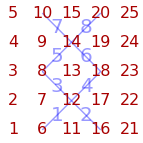

```mathematica
{vx,line}=GraphicPointLines[5,5,{{6,12},{16,12},{12,8},{12,18},{8,14},{18,14},{14,10},{14,20}}];
```

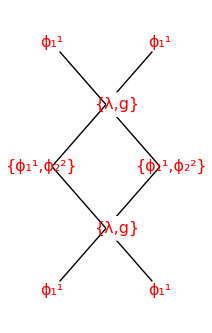

```mathematica
Graphics[{Thin,Black,Map[Line[#]&,line],
TextOver[ϕd[1],vx[[16]]],
TextOver[ϕd[1],vx[[6]]],
TextOver[ϕd[1],vx[[10]]],
TextOver[ϕd[1],vx[[20]]],
TextOver[{ϕd[1],ϕd[2]},vx[[8]]+{-.2,0}],
TextOver[{ϕd[1],ϕd[2]},vx[[18]]+{.2,0}],
TextOver[{λ,g},vx[[12]]+{.2,0}],
TextOver[{λ,g},vx[[14]]+{.2,0}]
}
]
```